# NV-center qubits

This virtual quantum device is inspired by devices reported by the Delft team:https://www.nature.com/articles/s41586-022-04819-6
The qubits are composed of electron spin (qubit 0), Nitorgen spin (qubit 1), and Carbon 13 spins (qubit  2, 3, ...)

## VQD setup

Set the main directory as the current directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink package
One may also use the off-line questlink.m file, change it to the location of the local file

```mathematica
Import["https://qtechtheory.org/questlink.m"]
```

This will download a binary file  quest_link from the repo; some error will show if the system tries to override the file

Use CreateLocalQuESTEnv[quest_link_file] to use the existing binary

```mathematica
CreateDownloadedQuESTEnv[];
```

Load the VQD package; must be loaded after QuESTlink is loaded

```mathematica
Get["../vqd.wl"]
```

## User device configuration

Qubit 0 indicates electron spin,and the rest are nuclear spins  C^13 and N^14 - if applicable
Time unit is second (s)
Frequency unit is  Hertz (Hz)

```mathematica
Options[NVCenterDelftN]={
QubitNum->6
,
(* T1 of each qubit *)
T1-> <|0-> 3600,1->60,2->60,3->60,4->60,5->60 |>
,
(* T2 of each qubit; we assume dynamical decoupling is actively applied *)
T2-> <|0-> 1.5,1->10,2->10,3->10,4->9,5->9|>
,
(* dipolar interaction among nuclear spins: cross-talk ZZ-coupling in order of a few Hz on passive noise *)
FreqWeakZZ->5
,
(* direct single rotation on Nuclear spin is done via RF, put electron in state -1 leave out the Rx Ry on nuclear spins ideally. *)
FreqSingleXY-> <|0->15*10^6,1->500 ,2->500,3->500,4->500,5->500|>
,
(* usually done virtually *)
FreqSingleZ-><|0->32*10^6,1->400*10^3,2->400*10^3,3->400*10^3,4->400*10^3,5->400*10^3|>
,
(* Frequency of CRot gate, conditional rotation done via dynamical decoupling or dd+RF. The gate is conditioned on electron spin state *)
FreqCRot-> <|1-> 1.5*10^3,2->2.8*10^3,3->0.8*10^3,4->2*10^3 ,5->2*10^3|>
,
(* Frequency of nitrogen controlled-Rx gate, where the nitrogen is the control qubit *)
FreqCRx -> 1.5 * 10^3
,
(* Fidelity of controlled-rx gate, where the nitrogen is the control qubit *)
FidCRx -> 0.9
,
(* Fidelity of CRot gate  *)
FidCRot-><|1-> 0.98,2->0.98, 3->0.98,4->0.98 ,5->0.98|>
,
(* fidelity of x- and y- rotations on each qubit *)
FidSingleXY-> <| 0->0.9995,1-> 0.995,2->0.995, 3->0.99,4->0.99,5->0.99 |>
,
(* fidelity of z- rotations on each qubit *)
FidSingleZ->  <| 0->0.9999,1-> 0.9999,2->0.99999, 3->0.9999,4->0.999,5->0.99 |>
,
(* over rotation δ in unit radian when applying physical single-qubit gates Rx and Ry. The noisy rotation will be Rx(θ+δ) *)
OverRotation -> <|0->0.001, 1->0.1, 2->0.01, 3->0.01, 4->0.01, 5->0.01 |>,
(* over rotation δ in unit radian when applying two-qubit gates where the control qubit is the electron spin. The numbers indicate the target qubits. Thus, for q=0, it means the two qubit gate between nuclear and electron spin *)
OverRotation2 ->  <|0->0.1, 1->0.001, 2->0.01, 3->0.01, 4->0.01, 5->0.01 |>
,
(* Error ratio of 1-qubit depolarising:dephasing of x- and y- rotations  *)
EFSingleXY->{0.75,0.25}
,
(* Error ratio of 2-qubit depolarising:dephasing of CRot and controlled-Rx gates  *)
EFCRot->{0.9,0.1}
,
(* initialization fidelity on the electron spin *)
FidInit-> 0.999
,
(* initialization duration on the electron spin *)
DurInit->2*10^-3
,
(* measurement fidelity on the electron spin *)
FidMeas->0.946
,
(* measurement duration on the electron spin *)
DurMeas->2*10^-5
};
```

## Elementary guide

### Native gates

Direct iIitialisation and measurement are on the NV electron spin only
Init_0, M_0

Single-qubit gates
Rx_q[θ], Ry_q[θ], Rz_q[θ] 

Two-qubit gates between electron(control) and nuclear spins(target) are conditional rotation, where  CRσ[θ]:=|0X0|⊗ Rσ[θ]+|1X1|⊗ Rσ[-θ]
CRx_(0,q)[θ], CRy_(0,q)[θ]

Two-qubit gate between Nitrogen(control) and electron spin(target) is the standard controlled-Rx
C_1[Rx_0[θ]]

others: doing nothing
Wait_q[duration]

### Common nuclear spin gates, obtained by sequence of native gates

```mathematica
cX::usage="Controlled-X gate sequence on NV-center";
cY::usage="Controlled-Y gate sequence on NV-center";
cZ::usage="Controlled-Z gate sequence on NV-center";
initNcl::usage="Nuclear spin qubit initialisation sequence on NV-center";
measZ::usage="Nuclear spin qubit measurement sequence on NV-center";
```

```mathematica
(* cotrolled-pauli gates, where control qubits are the electron spins *)
Subscript[cX, c_,t_] := Sequence @@ {Subscript[CRx, c,t][π/2],Subscript[Rz, c][-π/2],Subscript[Rx, t][-π/2]}
Subscript[cY, c_,t_] := Sequence @@ {Subscript[CRy, c,t][π/2],Subscript[Rz, c][-π/2],Subscript[Ry, t][-π/2]}
Subscript[cZ, c_,t_] := Sequence @@ {Subscript[Rx, t][π/2],Subscript[CRy, c,t][-π/2],Subscript[Rz, c][-π/2],Subscript[Ry, t][π/2],Subscript[Rx, t][-π/2]}
(* initialisation the nuclear spins *)
Subscript[initNcl, q_ /; q>0] :=Sequence @@ {Subscript[Init, 0],Subscript[Ry, 0][π/2],Subscript[CRx, 0,q][π/2],Subscript[Rx, 0][π/2],Subscript[CRy, 0,q][-π/2]}
(*measurement sequences on nuclear spins the computational basis *)
Subscript[measZ, q_ /; q>0] := Sequence[Subscript[Ry, 0][π/2],Subscript[Rx, q][π/2],Subscript[CRy, 0,q][-π/2],Subscript[Rx, 0][π/2],Subscript[M, 0]]
```

{Init_0,Ry_0[π/2],CRx_(0,1)[π/2],Rx_0[π/2],CRy_(0,1)[-π/2]}

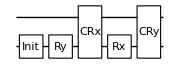

```mathematica
{Subscript[initNcl, 1]}
DrawCircuit@%
```

### Introducing explicit Nitrogen spin, over-rotations

```mathematica
?OverRotation2
```

Initialize all qubits to zero

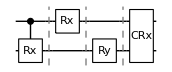

```mathematica
circ=List/@{Subscript[C, 1][Subscript[Rx, 0][θ]], Subscript[Rx, 1][θ], Subscript[Ry, 0][θ],Subscript[CRx, 0,1][θ]};
DrawCircuit[circ]
```

```mathematica
noisycirc=InsertCircuitNoise[circ, NVCenterDelftN[]]
```

{{0,{C_1[Rx_0[0.1+θ]],Depol_(0,1)[Min[15/16,0.0362502 Abs[θ]]],Deph_(0,1)[Min[3/4,0.0040278 Abs[θ]]]},{Depol_0[0.],Deph_0[0.],R[0.,Z_1 Z_2],R[0.,Z_1 Z_3],R[0.,Z_1 Z_4],R[0.,Z_1 Z_5],R[0.,Z_2 Z_3],R[0.,Z_2 Z_4],R[0.,Z_2 Z_5],R[0.,Z_3 Z_4],R[0.,Z_3 Z_5],R[0.,Z_4 Z_5],Depol_1[0.],Deph_1[0.],R[0.,Z_2 Z_3],R[0.,Z_2 Z_4],R[0.,Z_2 Z_5],R[0.,Z_3 Z_4],R[0.,Z_3 Z_5],R[0.,Z_4 Z_5],Depol_2[0.75 (1-ⅇ^(-0.0000111111 Abs[θ]))],Deph_2[0.5 (1-ⅇ^(-0.0000666667 Abs[θ]))],R[0.000133333 Abs[θ],Z_1 Z_3],R[0.000133333 Abs[θ],Z_1 Z_4],R[0.000133333 Abs[θ],Z_1 Z_5],R[0.000133333 Abs[θ],Z_3 Z_4],R[0.000133333 Abs[θ],Z_3 Z_5],R[0.000133333 Abs[θ],Z_4 Z_5],Depol_3[0.75 (1-ⅇ^(-0.0000111111 Abs[θ]))],Deph_3[0.5 (1-ⅇ^(-0.0000666667 Abs[θ]))],R[0.000133333 Abs[θ],Z_1 Z_2],R[0.000133333 Abs[θ],Z_1 Z_4],R[0.000133333 Abs[θ],Z_1 Z_5],R[0.000133333 Abs[θ],Z_2 Z_4],R[0.000133333 Abs[θ],Z_2 Z_5],R[0.000133333 Abs[θ],Z_4 Z_5],Depol_4[0.75 (1-ⅇ^(-0.0000111111 Abs[θ]))],Deph_4[0.5 (1-ⅇ^(-0.0000740741 Abs[θ]))],R[0.000133333 Abs[θ],Z_1 Z_2],R[0.000133333 Abs[θ],Z_1 Z_3],R[0.000133333 Abs[θ],Z_1 Z_5],R[0.000133333 Abs[θ],Z_2 Z_3],R[0.000133333 Abs[θ],Z_2 Z_5],R[0.000133333 Abs[θ],Z_3 Z_5],Depol_5[0.75 (1-ⅇ^(-0.0000111111 Abs[θ]))],Deph_5[0.5 (1-ⅇ^(-0.0000740741 Abs[θ]))],R[0.000133333 Abs[θ],Z_1 Z_2],R[0.000133333 Abs[θ],Z_1 Z_3],R[0.000133333 Abs[θ],Z_1 Z_4],R[0.000133333 Abs[θ],Z_2 Z_3],R[0.000133333 Abs[θ],Z_2 Z_4],R[0.000133333 Abs[θ],Z_3 Z_4]}},{0.000666667 Abs[θ],{Rx_1[0.1+θ],Depol_1[Min[0.75,0.00179386 Abs[θ]]],Deph_1[Min[0.5,0.000597954 Abs[θ]]]},{Depol_0[0.75 (1-ⅇ^(-Abs[θ]/1800000))],Deph_0[0.5 (1-ⅇ^(-0.00133333 Abs[θ]))],R[Abs[θ]/2500,Z_1 Z_2],R[Abs[θ]/2500,Z_1 Z_3],R[Abs[θ]/2500,Z_1 Z_4],R[Abs[θ]/2500,Z_1 Z_5],R[Abs[θ]/2500,Z_2 Z_3],R[Abs[θ]/2500,Z_2 Z_4],R[Abs[θ]/2500,Z_2 Z_5],R[Abs[θ]/2500,Z_3 Z_4],R[Abs[θ]/2500,Z_3 Z_5],R[Abs[θ]/2500,Z_4 Z_5],Depol_1[0.],Deph_1[0.],R[0,Z_2 Z_3],R[0,Z_2 Z_4],R[0,Z_2 Z_5],R[0,Z_3 Z_4],R[0,Z_3 Z_5],R[0,Z_4 Z_5],Depol_2[0.75 (1-ⅇ^(-Abs[θ]/30000))],Deph_2[0.5 (1-ⅇ^(-Abs[θ]/5000))],R[Abs[θ]/2500,Z_1 Z_3],R[Abs[θ]/2500,Z_1 Z_4],R[Abs[θ]/2500,Z_1 Z_5],R[Abs[θ]/2500,Z_3 Z_4],R[Abs[θ]/2500,Z_3 Z_5],R[Abs[θ]/2500,Z_4 Z_5],Depol_3[0.75 (1-ⅇ^(-Abs[θ]/30000))],Deph_3[0.5 (1-ⅇ^(-Abs[θ]/5000))],R[Abs[θ]/2500,Z_1 Z_2],R[Abs[θ]/2500,Z_1 Z_4],R[Abs[θ]/2500,Z_1 Z_5],R[Abs[θ]/2500,Z_2 Z_4],R[Abs[θ]/2500,Z_2 Z_5],R[Abs[θ]/2500,Z_4 Z_5],Depol_4[0.75 (1-ⅇ^(-Abs[θ]/30000))],Deph_4[0.5 (1-ⅇ^(-Abs[θ]/4500))],R[Abs[θ]/2500,Z_1 Z_2],R[Abs[θ]/2500,Z_1 Z_3],R[Abs[θ]/2500,Z_1 Z_5],R[Abs[θ]/2500,Z_2 Z_3],R[Abs[θ]/2500,Z_2 Z_5],R[Abs[θ]/2500,Z_3 Z_5],Depol_5[0.75 (1-ⅇ^(-Abs[θ]/30000))],Deph_5[0.5 (1-ⅇ^(-Abs[θ]/4500))],R[Abs[θ]/2500,Z_1 Z_2],R[Abs[θ]/2500,Z_1 Z_3],R[Abs[θ]/2500,Z_1 Z_4],R[Abs[θ]/2500,Z_2 Z_3],R[Abs[θ]/2500,Z_2 Z_4],R[Abs[θ]/2500,Z_3 Z_4]}},{0.00266667 Abs[θ],{Ry_0[0.001+θ],Depol_0[Min[0.75,0.000179083 Abs[θ]]],Deph_0[Min[0.5,0.0000596943 Abs[θ]]]},{Depol_0[0.],Deph_0[0.],R[0,Z_1 Z_2],R[0,Z_1 Z_3],R[0,Z_1 Z_4],R[0,Z_1 Z_5],R[0,Z_2 Z_3],R[0,Z_2 Z_4],R[0,Z_2 Z_5],R[0,Z_3 Z_4],R[0,Z_3 Z_5],R[0,Z_4 Z_5],Depol_1[0.75 (1-ⅇ^(-Abs[θ]/900000000))],Deph_1[0.5 (1-ⅇ^(-Abs[θ]/150000000))],R[Abs[θ]/75000000,Z_2 Z_3],R[Abs[θ]/75000000,Z_2 Z_4],R[Abs[θ]/75000000,Z_2 Z_5],R[Abs[θ]/75000000,Z_3 Z_4],R[Abs[θ]/75000000,Z_3 Z_5],R[Abs[θ]/75000000,Z_4 Z_5],Depol_2[0.75 (1-ⅇ^(-Abs[θ]/900000000))],Deph_2[0.5 (1-ⅇ^(-Abs[θ]/150000000))],R[Abs[θ]/75000000,Z_1 Z_3],R[Abs[θ]/75000000,Z_1 Z_4],R[Abs[θ]/75000000,Z_1 Z_5],R[Abs[θ]/75000000,Z_3 Z_4],R[Abs[θ]/75000000,Z_3 Z_5],R[Abs[θ]/75000000,Z_4 Z_5],Depol_3[0.75 (1-ⅇ^(-Abs[θ]/900000000))],Deph_3[0.5 (1-ⅇ^(-Abs[θ]/150000000))],R[Abs[θ]/75000000,Z_1 Z_2],R[Abs[θ]/75000000,Z_1 Z_4],R[Abs[θ]/75000000,Z_1 Z_5],R[Abs[θ]/75000000,Z_2 Z_4],R[Abs[θ]/75000000,Z_2 Z_5],R[Abs[θ]/75000000,Z_4 Z_5],Depol_4[0.75 (1-ⅇ^(-Abs[θ]/900000000))],Deph_4[0.5 (1-ⅇ^(-Abs[θ]/135000000))],R[Abs[θ]/75000000,Z_1 Z_2],R[Abs[θ]/75000000,Z_1 Z_3],R[Abs[θ]/75000000,Z_1 Z_5],R[Abs[θ]/75000000,Z_2 Z_3],R[Abs[θ]/75000000,Z_2 Z_5],R[Abs[θ]/75000000,Z_3 Z_5],Depol_5[0.75 (1-ⅇ^(-Abs[θ]/900000000))],Deph_5[0.5 (1-ⅇ^(-Abs[θ]/135000000))],R[Abs[θ]/75000000,Z_1 Z_2],R[Abs[θ]/75000000,Z_1 Z_3],R[Abs[θ]/75000000,Z_1 Z_4],R[Abs[θ]/75000000,Z_2 Z_3],R[Abs[θ]/75000000,Z_2 Z_4],R[Abs[θ]/75000000,Z_3 Z_4]}},{0.00266673 Abs[θ],{CRx_(0,1)[0.001+θ],Depol_(0,1)[Min[15/16,0.00717924 Abs[θ]]],Deph_(0,1)[Min[3/4,0.000797694 Abs[θ]]]},{Depol_0[0.],Deph_0[0.],R[0.,Z_1 Z_2],R[0.,Z_1 Z_3],R[0.,Z_1 Z_4],R[0.,Z_1 Z_5],R[0.,Z_2 Z_3],R[0.,Z_2 Z_4],R[0.,Z_2 Z_5],R[0.,Z_3 Z_4],R[0.,Z_3 Z_5],R[0.,Z_4 Z_5],Depol_1[0.],Deph_1[0.],R[0.,Z_2 Z_3],R[0.,Z_2 Z_4],R[0.,Z_2 Z_5],R[0.,Z_3 Z_4],R[0.,Z_3 Z_5],R[0.,Z_4 Z_5],Depol_2[0.75 (1-ⅇ^(-0.0000111111 Abs[θ]))],Deph_2[0.5 (1-ⅇ^(-0.0000666667 Abs[θ]))],R[0.000133333 Abs[θ],Z_1 Z_3],R[0.000133333 Abs[θ],Z_1 Z_4],R[0.000133333 Abs[θ],Z_1 Z_5],R[0.000133333 Abs[θ],Z_3 Z_4],R[0.000133333 Abs[θ],Z_3 Z_5],R[0.000133333 Abs[θ],Z_4 Z_5],Depol_3[0.75 (1-ⅇ^(-0.0000111111 Abs[θ]))],Deph_3[0.5 (1-ⅇ^(-0.0000666667 Abs[θ]))],R[0.000133333 Abs[θ],Z_1 Z_2],R[0.000133333 Abs[θ],Z_1 Z_4],R[0.000133333 Abs[θ],Z_1 Z_5],R[0.000133333 Abs[θ],Z_2 Z_4],R[0.000133333 Abs[θ],Z_2 Z_5],R[0.000133333 Abs[θ],Z_4 Z_5],Depol_4[0.75 (1-ⅇ^(-0.0000111111 Abs[θ]))],Deph_4[0.5 (1-ⅇ^(-0.0000740741 Abs[θ]))],R[0.000133333 Abs[θ],Z_1 Z_2],R[0.000133333 Abs[θ],Z_1 Z_3],R[0.000133333 Abs[θ],Z_1 Z_5],R[0.000133333 Abs[θ],Z_2 Z_3],R[0.000133333 Abs[θ],Z_2 Z_5],R[0.000133333 Abs[θ],Z_3 Z_5],Depol_5[0.75 (1-ⅇ^(-0.0000111111 Abs[θ]))],Deph_5[0.5 (1-ⅇ^(-0.0000740741 Abs[θ]))],R[0.000133333 Abs[θ],Z_1 Z_2],R[0.000133333 Abs[θ],Z_1 Z_3],R[0.000133333 Abs[θ],Z_1 Z_4],R[0.000133333 Abs[θ],Z_2 Z_3],R[0.000133333 Abs[θ],Z_2 Z_4],R[0.000133333 Abs[θ],Z_3 Z_4]}},{0.0033334 Abs[θ],{},{}}}

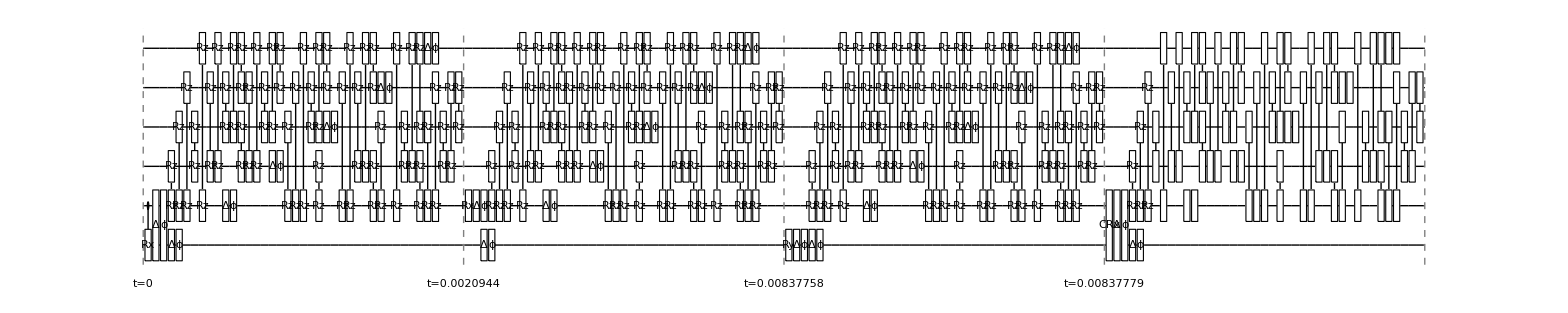

```mathematica
DrawCircuit @ (noisycirc/.θ->π)
```